# Degrees of Freedom in a Cooling Universe

### Clearing up variables

```mathematica
Clear[F,g,Tc,Species,Quarks,Pions,T,m,P]
Off[NIntegrate::slwcon ]
Off[NIntegrate::ncvb]
Off[NIntegrate::inumr]
```

### Defining the density integral for a particular species

```mathematica
F[T_,m_,g_,P_]:=g*NIntegrate[(u^2*(u^2-m/T)^(1/2))/(ⅇ^u+(-1)^(P+1)),{u,m/T,∞},PrecisionGoal->2];
```

### Defining the relevant particles and the QCD confinement temperature

```mathematica
Tc=.150;
Species={{0,2,0},{.511*10^-3,4,1},{.1057,4,1},{1.777,4,1},{10^-10,3,1},{80.4,6,0},{91.2,3,0},{125,1,0}};
Quarks={{2*10^-3,12,1},{5*10^-3,12,1},{.1,12,1},{1.25,12,1},{4.2,12,1},{174.2,12,1},{0,16,0}};
Pions={{.139,2,0},{.135,1,0}};
```

### Defining the degrees of freedom function

```mathematica
g=Function[{T},Sum[F[T,Species[[i,1]],Species[[i,2]],Species[[i,3]]],{i,1,Length[Species]}]+.5(1+Tanh[20(-Tc+T)])*Sum[F[T,Quarks[[i,1]],Quarks[[i,2]],Quarks[[i,3]]],{i,1,Length[Quarks]}]+.5(1+Tanh[20*(Tc-T)])*Sum[F[T,Pions[[i,1]],Pions[[i,2]],Pions[[i,3]]],{i,1,Length[Pions]}]];
```

### PPlotting the degrees of freedom vs. Temperature

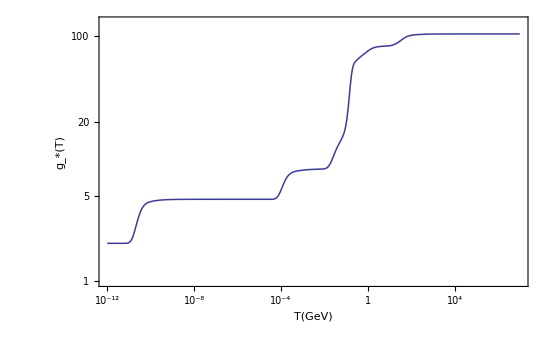

```mathematica
LogLogPlot[15/π^4*Re[g[T]],{T,10^-12, 10^7},PlotRange->{{10^-12,10^7},{10^0,1.3*10^2}},Frame->True,FrameLabel->{"T(GeV)","g_*(T)"},PlotStyle->{Thickness[.002]},Exclusions->None]
```